```mathematica
Clear[k];DS=DSolve[{p'[t]==(k*Cos[t])*p[t],p[0]==p0},p[t],t]
```

{{p[t]→ⅇ^(k Sin[t]) p0}}

```mathematica
y1[t_]=DS[[1,1,2]];
m1=p0+p0*0.1
```

1.1 p0

```mathematica
m2=Solve[y1[1]==m1,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→0.113266}}

```mathematica
y2[t_]=y1[t]/.k->m2[[1,1,2]]
```

ⅇ^(0.113266 Sin[t]) p0

```mathematica
y3[t_]=y2[t]/.p0->100
y4[t_]=y2[t]/.p0->500
y5[t_]=y2[t]/.p0->1000
```

100 ⅇ^(0.113266 Sin[t])

500 ⅇ^(0.113266 Sin[t])

1000 ⅇ^(0.113266 Sin[t])

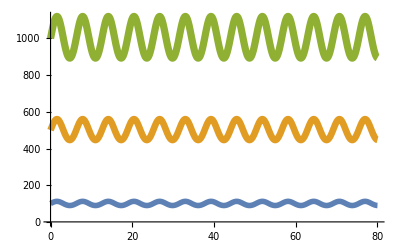

```mathematica
Plot[{y3[t],y4[t],y5[t]},{t,0,80},
PlotStyle->{Thickness[0.01],Thickness[0.012],
Thickness[0.013]}]
```